# 3D MOT beam power fits

#### 2019.07.12 Measured powers in the box for each arm, and corresponding I2V voltages. {voltage [mV],power [μW], }.

```mathematica
X1 = {{280,340},{200,260},{126,160},{72,90}};
X2 = {{369,310},{252,220},{140,120},{48,40}};
Y1 = {{580,620},{436,460},{236,250},{64,90}};
Y2 = {{624,600},{472,450},{312,300},{136,135}};
Z1 = {{660,108},{536,88},{280,46},{104,08}};
Z2 = {{111,87},{92,74},{60.8,49},{32,28.5}};
```

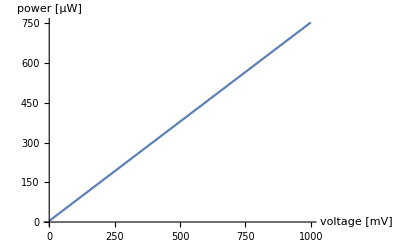

4.25002+0.748817 x

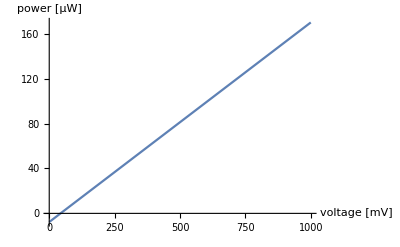

-7.69206+0.177701 x

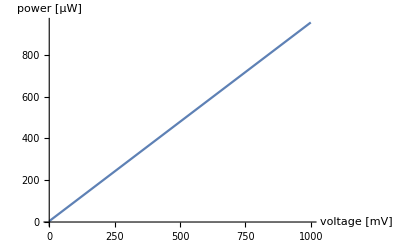

4.15586+0.951021 x

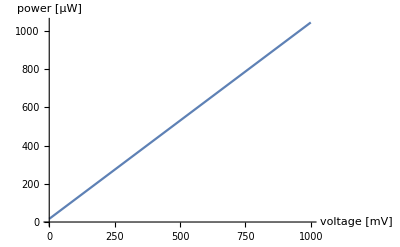

16.5242+1.0288 x

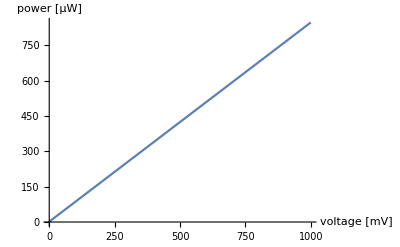

1.49123+0.845532 x

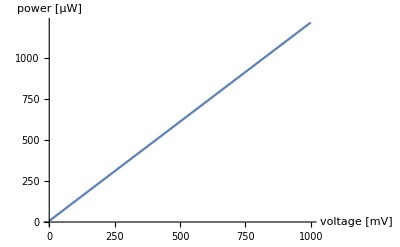

6.90207+1.21297 x

```mathematica
Data ={X1,X2,Y1,Y2,Z1,Z2};
For[i=1,i<Length[Data]+1,i++,
Print[Fit[Data[[i]],{1,x},{x}]];
Print[Plot[Evaluate[Fit[Data[[i]],{1,x},{x}]],{x,0,1000},AxesLabel->{"voltage [mV]","power [μW]"}]]
]
```

#### 2019.07.29 Measured powers in the box for each arm, and corresponding I2V voltages. {voltage [mV], power [μW], }.